# Gravity

A bunch of the tools we are looking at were developed to think about planetary motion

Newton’s Laws

For each body F_i=m_i a_i=m_i p''_i
For each planet F_i=C m_i∑_(j=1)^n m_j(p_i-p_j)/(||p_i-p_j(||)^3)

We are going to build the equations and look at some orbits.  We need to decide how we are going to store the positions of all the planets. We need to decide if we are going to solve a first order system or a second order system of half the size.

### Code:

```mathematica
fG[{m1_,p1_},{m2_,p2_}]:= Module[{r=Norm[p1-p2],Tol=10^-12,G=1.0 },
(* in MKS units G=6.67*10^-11 *)
If[r<Tol,0,-G *m1*m2*(p1-p2)/r^3]]

FG[ms_,ps_List]:= Module[{n=Length[ms]},
Table[ 1/ms⟦i⟧Sum[fG[{ms⟦i⟧,ps⟦i⟧},{ms⟦j⟧,ps⟦j⟧}],{j,1,n}],{i,n}]
]
```

Here is a picture of some positions with the gravitational forces.  It is a good idea to check with a picture you have the signs correct.

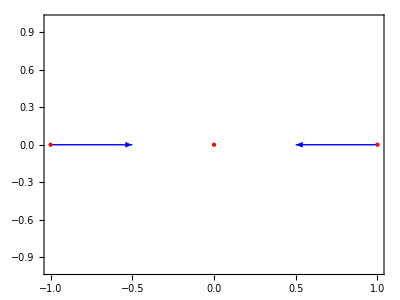

```mathematica
ms={1,1,1};
ps={{-1,0},{0,0},{1,0}};
Fs=FG[ms,ps];
ϵ=0.4;
n=Length[ms];
Graphics[
Table[{
{Blue,Arrow[{ps[[i]],ps[[i]]+ϵ Fs⟦i⟧}]},
{Red,Point[ps⟦i⟧]}
},{i,n}],
Frame->True]
```

## Big Moon: Elliptical Orbit

The earth is about 80 times more massive than the moon. We should probably fix some of the constants in this system!

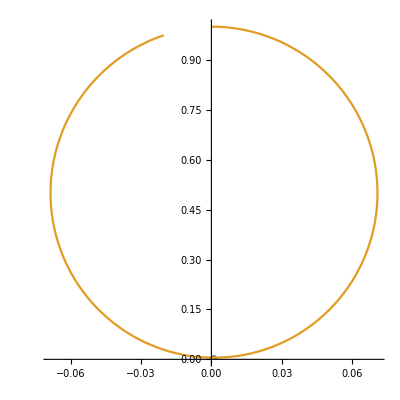

```mathematica
Clear[ps,t]
ms={100,1};
ps0={{0,0},{0,1}};
vs0={{0,0},{1,0}};
TMax=0.2;
pSol=NDSolveValue[ {ps''[t]==FG[ms,ps[t]],ps[0]==ps0,ps'[0]==vs0},ps,{t,0,TMax}];
ParametricPlot[{pSol[t]⟦1⟧,pSol[t]⟦2⟧},{t, 0, TMax},PlotPoints->100,AspectRatio->1]
```

## Identical Suns: Figure Eight Orbit

## Identical Suns + Planet: Figure Eight Orbit